```mathematica
(*Go to https://melt1.notion.site/ to download the files*)
```

```mathematica
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"]
```

```mathematica
<<"C:/Users/35386/Documents/melt/melt.m"(*Use your own path*)
```

```mathematica
NotebookOpen[$UserBaseDirectory<>"/Kernel/init.m"](*Use this to open the Mathematica initialization file, you can use this to load the melt package every time you open mathematica*)
```

```mathematica
NotebookOpen["C:/Users/35386/Documents/melt/melt.nb"](*This will open the melt notebook where you can view all of the function included in the package*)
```

```mathematica
LoadPauliMatrices[]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]

```mathematica
(*We can use the ? command to check what a specific input does and what inputs it takes*)
```

```mathematica
?LoadPauliMatrices
```

```mathematica
σx//mf
```

(0 | 1
1 | 0)

{{0,1},{1,0}}

```mathematica
?mf
```

```mathematica
σz
```

{{1,0},{0,-1}}

## Transverse field ising model

```mathematica
dimlist = Table[i,{i,2,9}];
J = 1.;
glist= logspace[-2,2,50];
Do[
do[
H =-J Total[Table[KronEye[σz,dim,i].KronEye[σz,dim,i+1],{i,1,dim-1}]] - J*g Total[Table[KronEye[σx,dim,i],{i,1,dim}]];
gs = Quiet@Eigvecs[H][[All,1]];
mag[g,dim] = Total[Table[Abs[gs[[i+1]]]^2*Abs[2Total[IntegerDigits[i,2]]/dim-1],{i,0,2^dim-1}]];,
{g,glist}],
{dim,dimlist}]
```

0h : 0m : 0s

0h : 0m : 0s

0h : 0m : 0s

0h : 0m : 1s

0h : 0m : 0s

0h : 0m : 0s

0h : 0m : 1s

0h : 0m : 3s

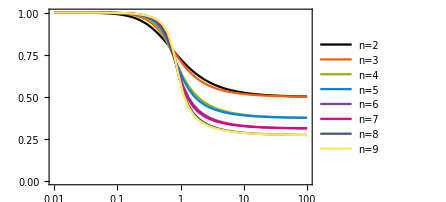

```mathematica
ListLogLinearPlot[Table[{g,mag[g,dim]},{dim,dimlist},{g,glist}],Joined->True,PlotRange->{{10^-2,10^2},{0,1}},PlotLegends->legend[Table["n="<>ToString[dim],{dim,dimlist}],{0.2,0.5},FontSize->10],FrameTicks->{{Automatic,None},{logticks[-2,2,1],None}},PlotStyle->COLORLIST]
```

### Additional notes

#### Making the Hamiltonian

```mathematica
?KronEye
```

```mathematica
kron[σz,σz,σ0,σ0]-KronEye[σz,4,1].KronEye[σz,4,2]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

#### Calculating the ground state

```mathematica
dimtest = 6;
Jtest=1.;
gtest = 1.;
Htest =-Jtest Total[Table[KronEye[σz,dimtest,i].KronEye[σz,dimtest,i+1],{i,1,dimtest-1}]] - Jtest*gtest Total[Table[KronEye[σx,dimtest,i],{i,1,dimtest}]];
```

```mathematica
Eigenvectors[Htest][[All,1]]//Chop
```

{0.206268,-0.0472048,0.0223261,-0.22679,0.0264108,0.154475,0.0226249,0.0322839,-0.0531382,0.154475,0.313421,0,-0.0082184,-0.290441,-0.294328,-0.00657909,-0.210892,0.0413245,-0.122266,0.0654349,-0.145498,0.125961,-0.324735,0,0.056417,-0.124469,-0.166201,-0.0425389,0,-0.0219714,0.00277166,0.265882,-0.0274256,-0.0366787,0.0304077,0.0636816,0,-0.138073,-0.0327778,0.235876,-0.15088,0.0217877,-0.147241,-0.101875,-0.0702607,0,0.0665598,0.0551799,0,0,0.0908685,-0.107153,-0.0359423,-0.0164055,0.0531382,-0.124469,0.147753,0,-0.0449198,-0.056417,-0.00545426,-0.184431,0.0264108,0.0449198}

```mathematica
Eigvecs[Htest][[All,1]]
```

{0.400548,0.206268,0.130935,0.166201,0.122672,0.0748228,0.0952466,0.156542,0.122672,0.0670863,0.0472048,0.0676192,0.0874638,0.0615667,0.0911072,0.166201,0.130935,0.0695418,0.0456557,0.0615667,0.0472048,0.031159,0.0425389,0.0748228,0.0952466,0.0558988,0.0425389,0.0670863,0.0911072,0.0695418,0.107974,0.206268,0.206268,0.107974,0.0695418,0.0911072,0.0670863,0.0425389,0.0558988,0.0952466,0.0748228,0.0425389,0.031159,0.0472048,0.0615667,0.0456557,0.0695418,0.130935,0.166201,0.0911072,0.0615667,0.0874638,0.0676192,0.0472048,0.0670863,0.122672,0.156542,0.0952466,0.0748228,0.122672,0.166201,0.130935,0.206268,0.400548}

```mathematica
(*These clearly don't agree, why is that?*)
```

```mathematica
Eigenvalues[Htest]
```

{-7.29623,7.29623,-6.81408,6.81408,5.87781,-5.87781,5.39566,-5.39566,5.02397,-5.02397,-4.54182,4.54182,4.30219,-4.30219,3.82004,-3.82004,3.75441,-3.75441,-3.60555,3.60555,-3.41246,3.41246,3.27226,-3.27226,3.1234,-3.1234,2.93032,-2.93032,-2.88377,2.88377,-2.40162,2.40162,2.33599,-2.33599,-2.02993,2.02993,-1.99404,1.99404,1.85384,-1.85384,-1.54778,1.54778,1.5119,-1.5119,1.48215,-1.48215,-1.1402,1.1402,-1.,1.,-0.760363,0.760363,0.658057,-0.658057,0.611508,-0.611508,-0.41842,0.41842,-0.278216,0.278216,0.129362,-0.129362,-0.0637272,0.0637272}

```mathematica
Eigvals[Htest]
```

{-7.29623,-6.81408,-5.87781,-5.39566,-5.02397,-4.54182,-4.30219,-3.82004,-3.75441,-3.60555,-3.41246,-3.27226,-3.1234,-2.93032,-2.88377,-2.40162,-2.33599,-2.02993,-1.99404,-1.85384,-1.54778,-1.5119,-1.48215,-1.1402,-1.,-0.760363,-0.658057,-0.611508,-0.41842,-0.278216,-0.129362,-0.0637272,0.0637272,0.129362,0.278216,0.41842,0.611508,0.658057,0.760363,1.,1.1402,1.48215,1.5119,1.54778,1.85384,1.99404,2.02993,2.33599,2.40162,2.88377,2.93032,3.1234,3.27226,3.41246,3.60555,3.75441,3.82004,4.30219,4.54182,5.02397,5.39566,5.87781,6.81408,7.29623}

```mathematica
(*Eigvals orders the eigenvalues and eigenvectors by smallest to largest while Eigenvalues orders them by absolute value. So for numerics it is best to us Eigvals*)
```

```mathematica
GroundState[Htest](*We could also use the Groundstate function from melt but it only gives an approximate answer and sometimes struggles with degenerate ground states*)
```

{0.400574,0.206299,0.130934,0.166224,0.122675,0.0748026,0.0952315,0.156484,0.122664,0.0670917,0.0472074,0.067629,0.0874574,0.0615744,0.0910927,0.16615,0.130936,0.0695351,0.045652,0.0615868,0.0472061,0.0311927,0.0425571,0.0748286,0.0952473,0.0559289,0.0425339,0.0670948,0.0911257,0.069562,0.107992,0.2063,0.206258,0.107987,0.069536,0.0911003,0.0670755,0.0425247,0.0558827,0.0952242,0.0748047,0.042525,0.0311677,0.0472101,0.0615463,0.0456615,0.0695204,0.130897,0.166175,0.0911025,0.0615633,0.0874638,0.067626,0.0472029,0.0670903,0.122706,0.156508,0.0952522,0.0747972,0.122666,0.166164,0.130948,0.20624,0.400591}

#### Why Eigvecs[Htest][[All, 1]] instead of Eigvecs[H][[1]]?

```mathematica
dimtest = 4;
Jtest=1.;
gtest = 1.;
Htest =-Jtest Total[Table[KronEye[σz,dimtest,i].KronEye[σz,dimtest,i+1],{i,1,dimtest-1}]] - Jtest*gtest Total[Table[KronEye[σx,dimtest,i],{i,1,dimtest}]];
```

```mathematica
(*I guess eigenvectors are output in the columns so that the diagonalization formula works as below*)
```

```mathematica
ConjugateTranspose[Eigvecs[Htest]].Htest.Eigvecs[Htest]//mf
```

(-4.75877 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -4.06418 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2.75877 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2.06418 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.69459 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.305407 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.305407 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.69459 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.06418 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.75877 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.06418 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.75877)

{{-4.75877,6.98006×10^-15,-2.55318×10^-16,-3.39804×10^-15,9.70937×10^-16,2.59208×10^-16,2.49487×10^-16,9.78022×10^-16,-2.94831×10^-16,1.66618×10^-16,1.15436×10^-15,1.59446×10^-16,1.33274×10^-15,2.23561×10^-15,-3.92508×10^-16,-1.0172×10^-15},{6.79281×10^-15,-4.06418,-3.92473×10^-16,-4.15707×10^-15,2.80458×10^-15,-1.76809×10^-16,-5.50089×10^-18,1.21766×10^-15,-4.9933×10^-16,2.12506×10^-16,8.2827×10^-16,1.20285×10^-16,1.22078×10^-15,1.86474×10^-15,-4.08578×10^-16,-8.48164×10^-16},{-3.04111×10^-16,-2.09171×10^-16,-2.75877,-3.68559×10^-16,3.13882×10^-16,-3.42938×10^-16,-5.52494×10^-16,-3.12969×10^-16,4.14831×10^-17,-1.37297×10^-16,-1.07389×10^-16,4.48242×10^-17,1.69911×10^-16,1.06647×10^-16,-8.66605×10^-17,-3.54636×10^-16},{-3.27142×10^-15,-4.29682×10^-15,-2.11004×10^-16,-2.06418,7.81502×10^-15,-2.2692×10^-16,7.95082×10^-17,2.9951×10^-17,-5.83864×10^-16,1.86157×10^-16,-3.44575×10^-15,-1.40022×10^-16,-3.24273×10^-16,-3.09313×10^-16,4.44901×10^-16,-4.34626×10^-16},{1.10491×10^-15,2.83364×10^-15,2.40589×10^-16,7.88647×10^-15,-1.69459,-4.82536×10^-16,-1.25833×10^-16,-3.81867×10^-15,1.67592×10^-15,2.29162×10^-16,2.05056×10^-16,1.49817×10^-17,5.30298×10^-16,1.99484×10^-15,3.44996×10^-16,1.57176×10^-17},{1.07934×10^-16,-2.44731×10^-16,-3.40888×10^-16,-1.69573×10^-16,-4.15386×10^-16,-1.,-3.70895×10^-17,4.30875×10^-17,-1.23377×10^-16,1.07922×10^-16,-2.95804×10^-16,-3.13058×10^-16,4.17443×10^-16,-1.61144×10^-16,2.16332×10^-16,-2.02266×10^-16},{6.25017×10^-17,-3.21848×10^-18,-5.51907×10^-16,5.95254×10^-17,-2.59196×10^-17,-5.35961×10^-17,-1.,-1.91684×10^-17,-2.3709×10^-16,-3.54603×10^-16,-2.48864×10^-17,-3.30025×10^-15,-4.74914×10^-17,-1.60588×10^-16,3.10152×10^-16,3.68732×10^-16},{7.95246×10^-16,1.22832×10^-15,-2.55669×10^-16,4.47703×10^-18,-3.76839×10^-15,1.66682×10^-16,-2.97119×10^-18,-0.305407,-1.16055×10^-15,1.33021×10^-17,8.76189×10^-16,-4.87695×10^-17,1.40022×10^-15,2.03496×10^-15,-3.40391×10^-17,1.06339×10^-16},{-3.31053×10^-16,-5.61726×10^-16,1.01209×10^-16,-5.19764×10^-16,1.75421×10^-15,-6.68235×10^-17,-2.24115×10^-16,-1.20358×10^-15,0.305407,-9.71409×10^-17,-7.58362×10^-16,5.43906×10^-18,-2.04378×10^-15,-5.87703×10^-16,-1.07679×10^-16,-6.22194×10^-17},{1.64225×10^-16,2.29244×10^-16,-9.42914×10^-17,1.73594×10^-16,2.47638×10^-16,1.08844×10^-16,-2.86311×10^-16,-6.63485×10^-18,-4.57803×10^-18,1.,1.52619×10^-17,1.42665×10^-16,4.36867×10^-16,4.20703×10^-16,4.05205×10^-16,3.22137×10^-16},{9.34106×10^-16,9.28096×10^-16,-9.41015×10^-17,-3.40656×10^-15,1.7139×10^-16,-2.8483×10^-16,-3.5322×10^-17,8.55367×10^-16,-6.20712×10^-16,-8.52065×10^-17,1.,-4.31452×10^-17,-1.6352×10^-15,-1.11843×10^-15,1.30617×10^-16,-1.11775×10^-15},{3.70576×10^-17,1.7544×10^-16,1.29497×10^-16,-1.58528×10^-17,6.6755×10^-18,-3.09254×10^-16,-3.2299×10^-15,-9.16302×10^-17,-9.05021×10^-17,1.13376×10^-16,1.74232×10^-17,1.69459,1.42827×10^-16,3.69178×10^-18,-1.06945×10^-15,1.75008×10^-16},{1.37194×10^-15,1.17963×10^-15,1.4191×10^-16,-2.91734×10^-16,5.26755×10^-16,4.50158×10^-16,-7.4156×10^-18,1.40477×10^-15,-2.03912×10^-15,3.94987×10^-16,-1.62963×10^-15,2.13725×10^-16,2.06418,4.81072×10^-16,-5.03034×10^-18,-5.56309×10^-16},{2.21768×10^-15,1.94361×10^-15,6.19598×10^-17,-2.03228×10^-16,2.05282×10^-15,-9.50499×10^-17,-1.77878×10^-16,1.98822×10^-15,-5.83322×10^-16,4.27225×10^-16,-1.05963×10^-15,2.38448×10^-17,5.32404×10^-16,2.75877,-1.34971×10^-16,-5.20507×10^-16},{-4.55748×10^-16,-3.6209×10^-16,-1.0872×10^-16,4.37214×10^-16,4.1906×10^-16,2.6533×10^-16,3.48141×10^-16,2.26354×10^-17,1.53063×10^-17,4.16444×10^-16,4.28561×10^-17,-1.08304×10^-15,5.62882×10^-17,-1.25618×10^-16,4.06418,-3.02073×10^-16},{-1.00435×10^-15,-9.21588×10^-16,-4.79317×10^-16,-5.14343×10^-16,-1.26526×10^-16,-2.10373×10^-16,1.82899×10^-16,1.94914×10^-16,9.92294×10^-17,4.35707×10^-16,-1.32759×10^-15,7.0795×10^-17,-8.67694×10^-16,-4.50121×10^-16,-3.3339×10^-16,4.75877}}

#### Calculating the magnetization

```mathematica
dimtest = 6;
Jtest=1.;
gtest = 1000.;
Htest =-Jtest Total[Table[KronEye[σz,dimtest,i].KronEye[σz,dimtest,i+1],{i,1,dimtest-1}]] - Jtest*gtest Total[Table[KronEye[σx,dimtest,i],{i,1,dimtest}]];
gstest = Eigvecs[Htest][[All,1]];
```

```mathematica
Abs[gstest]^2
```

{0.0156641,0.0156484,0.0156328,0.0156484,0.0156328,0.0156172,0.0156328,0.0156484,0.0156328,0.0156172,0.0156016,0.0156172,0.0156328,0.0156172,0.0156328,0.0156484,0.0156328,0.0156172,0.0156016,0.0156172,0.0156016,0.015586,0.0156016,0.0156172,0.0156328,0.0156172,0.0156016,0.0156172,0.0156328,0.0156172,0.0156328,0.0156484,0.0156484,0.0156328,0.0156172,0.0156328,0.0156172,0.0156016,0.0156172,0.0156328,0.0156172,0.0156016,0.015586,0.0156016,0.0156172,0.0156016,0.0156172,0.0156328,0.0156484,0.0156328,0.0156172,0.0156328,0.0156172,0.0156016,0.0156172,0.0156328,0.0156484,0.0156328,0.0156172,0.0156328,0.0156484,0.0156328,0.0156484,0.0156641}

```mathematica
(*The basis that our Hamiltonian is represented in it given by the Kronnecker product of all possible combinations of spin up and spin down. This is decided by the basis of our Pauli matrices*)
```

```mathematica
(*In order to figure out what combination of spin ups and down each entry is we can represent the number entry in the eigenvector as a binary number*)
```

```mathematica
IntegerDigits[34,2](*For example the 34th entry corresponds to this binary number which would be represented by the state below (0s and 1s might be opposite)*)
```

{1,0,0,0,1,0}

|1>⊗ |0> ⊗|0> ⊗|0> ⊗|1> ⊗|0>

```mathematica
(*The magnetization is essentially the absolute difference between the number of spin ups and spin downs in the state divided by the total number of spins. One way to calculate this is show below*)
```

```mathematica
Abs[2Total[IntegerDigits[34,2]]/dimtest-1]
```

1/3

```mathematica
(*We then need to average the magnetization of each state of the probability of being in that state which is given by Abs[gstest[[i+1]]]^2. The i+1 is because Mathematica starts counting at 1 but we need to start at 0 for the binary*)
```

```mathematica
magtest = Total[Table[Abs[gstest[[i+1]]]^2*Abs[2Total[IntegerDigits[i,2]]/dimtest-1],{i,0,2^dimtest-1}]]
```

0.312656

#### Logspace

```mathematica
?logspace
```

```mathematica
?linspace
```

```mathematica
linspace[0,1,101]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
logspace[-2,2,50](*Gives points equally spaced on a log scale*)
```

{0.01,0.0120679,0.0145635,0.0175751,0.0212095,0.0255955,0.0308884,0.0372759,0.0449843,0.0542868,0.0655129,0.0790604,0.0954095,0.11514,0.13895,0.167683,0.202359,0.244205,0.294705,0.355648,0.429193,0.517947,0.625055,0.754312,0.910298,1.09854,1.32571,1.59986,1.9307,2.32995,2.81177,3.39322,4.09492,4.94171,5.96362,7.19686,8.68511,10.4811,12.6486,15.2642,18.4207,22.23,26.827,32.3746,39.0694,47.1487,56.8987,68.6649,82.8643,100.}